=== Full symbolic T(phi, delta, alpha) ===

1/4 ⅇ^Im[delta] Abs[(1+ⅇ^(ⅈ delta)) Cos[alpha]+(-1+ⅇ^(ⅈ delta)) Cos[alpha-2 phi]]^2

1/4 ⅇ^Im[delta] Abs[(1+ⅇ^(ⅈ delta)) Cos[alpha]+(-1+ⅇ^(ⅈ delta)) Cos[alpha-2 phi]]^2

=== Perfect HWP (delta = Pi), aligned PBS (alpha = 0) ===

Abs[Cos[2 phi]]^2

=== Perfect HWP, PBS misaligned by alpha ===

Abs[Cos[alpha-2 phi]]^2

=== Retardance error: delta = Pi - eps, expand to order eps^2 ===

1/4 ⅇ^(-Im[eps]) Abs[1+ⅇ^(ⅈ (-eps+π))+(-1+ⅇ^(ⅈ (-eps+π))) Cos[2 phi]]^2

1/4 ⅇ^(-Im[eps]) Abs[2 ⅇ^(-ⅈ eps) Cos[phi]^2-2 Sin[phi]^2]^2

1/4 ⅇ^(-Im[eps]) Abs[2 ⅇ^(-ⅈ eps) Cos[phi]^2-2 Sin[phi]^2]^2

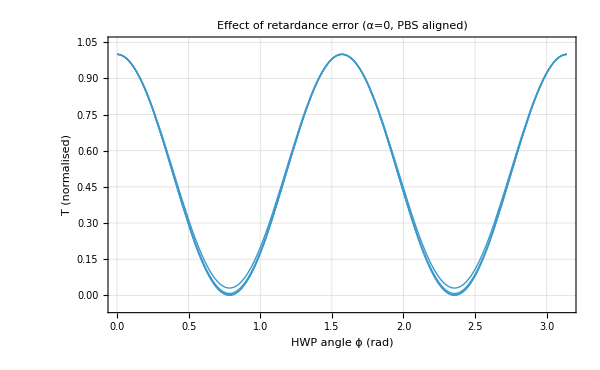

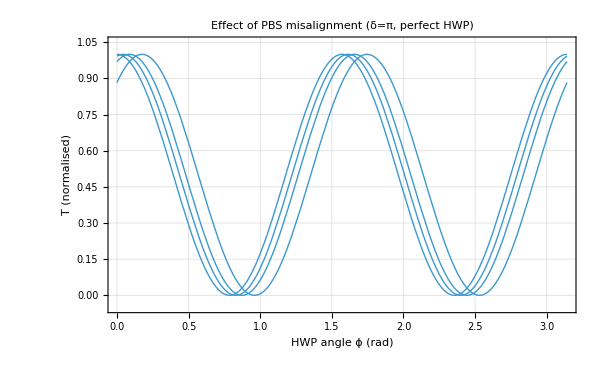

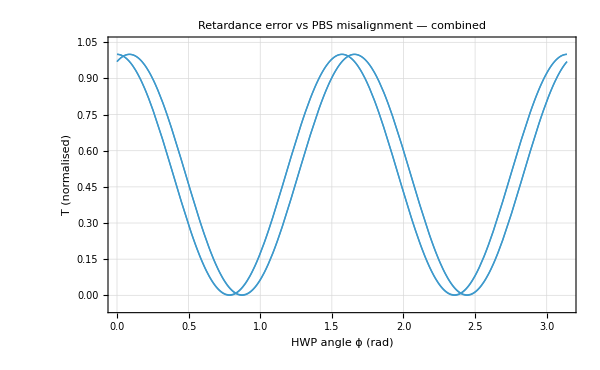

=== T_min = eps^2/4  and  ER = 4/eps^2 ===

Power::infy: Infinite expression 1/0 encountered.

delta (deg) | eps (deg) | T_min | ER
180 | 0 | 0 | ComplexInfinity
175 | 5 | 0.001904 | 525.2
170 | 10 | 0.007615 | 131.3
165 | 15 | 0.01713 | 58.36
160 | 20 | 0.03046 | 32.83

=== Key result: PBS misalignment vs retardance error ===

PBS misalignment alpha:  T = cos^2(2*phi - alpha)

-> only shifts the phase by 2*alpha

-> T_min = 0 always (cannot be confused with retardance error)

Retardance error eps:    T_min = eps^2/4  > 0

-> raises the floor, reduces contrast

-> completely different signature -- the two effects are distinguishable!

```mathematica
(* =========================================================================
   HWP + PBS Jones calculus
   Setup: horizontal input -> HWP(phi, delta) -> PBS(alpha) -> detector

   phi   : HWP fast-axis angle (what you rotate in the experiment)
   delta : HWP retardance  (Pi = perfect half-wave plate)
   alpha : PBS transmission axis angle from horizontal (0 = perfectly aligned)
   ========================================================================= *)

(* --- Helper definitions -------------------------------------------------- *)

(* 2D rotation matrix *)
RotMat[a_] := {{Cos[a], Sin[a]}, {-Sin[a], Cos[a]}}

(* Waveplate Jones matrix: fast axis at phi, retardance delta *)
WavePlate[phi_, delta_] :=
  RotMat[-phi] . {{Exp[I delta/2], 0}, {0, Exp[-I delta/2]}} . RotMat[phi]

(* PBS projection vector: transmits polarisation at angle alpha *)
PBSvec[alpha_] := {Cos[alpha], Sin[alpha]}

(* Horizontal input polarisation *)
Ein = {1, 0};

(* Transmitted intensity: project output onto PBS axis *)
TIntensity[phi_, delta_, alpha_] :=
  Abs[PBSvec[alpha] . WavePlate[phi, delta] . Ein]^2


(*---Symbolic results----------------------------------------------------*)Print["=== Full symbolic T(ϕ, δ, α) ==="]
TSymbolic=FullSimplify[TIntensity[phi,delta,alpha]]//TraditionalForm

Print["=== Perfect HWP (δ=π), aligned PBS (α=0) ==="]
FullSimplify[TSymbolic/. {delta->Pi,alpha->0}]//TraditionalForm
(*Expect:cos^2(2ϕ)*)

Print["=== Perfect HWP, PBS misaligned by α ==="]
FullSimplify[TSymbolic/. delta->Pi]//TraditionalForm
(*Expect:cos^2(2ϕ-α)-- phase shift only,T_min still 0*)

Print["=== Retardance error: δ = π - ϵ, to order ϵ^2 ==="]
TPerturbed=TSymbolic/. {alpha->0,delta->Pi-eps}
Series[TPerturbed,{eps,0,2}]//FullSimplify//TraditionalForm
(*Expect:(1/2+ϵ^2/8)+(1/2-ϵ^2/8) cos(4ϕ)*)


(* --- Numerical plots ------------------------------------------------------- *)

(* Figure 1: Retardance error effect, PBS aligned *)
deltaValues = {Pi, 175 Degree, 170 Degree, 160 Degree};
labels1 = {"δ=180°", "δ=175°",
           "δ=170°", "δ=160°"};

curves1 = Table[
  Plot[TIntensity[phi, dv, 0], {phi, 0, Pi},
    PlotStyle -> Thick,
    PlotRange -> {-0.05, 1.05}],
  {dv, deltaValues}];

fig1 = Show[curves1,
  PlotLabel -> Style["Effect of retardance error  (α=0, PBS aligned)", 14, Bold],
  AxesLabel -> {"HWP angle ϕ (rad)", "T (normalised)"},
  PlotLegends -> LineLegend[labels1],
  Frame -> True, GridLines -> Automatic,
  ImageSize -> 600]

(* Figure 2: PBS misalignment effect, perfect HWP *)
alphaValues = {0, 5 Degree, 10 Degree, 20 Degree};
labels2 = {"α=0°", "α=5°",
           "α=10°", "α=20°"};

curves2 = Table[
  Plot[TIntensity[phi, Pi, av], {phi, 0, Pi},
    PlotStyle -> Thick,
    PlotRange -> {-0.05, 1.05}],
  {av, alphaValues}];

fig2 = Show[curves2,
  PlotLabel -> Style["Effect of PBS misalignment  (δ=π, perfect HWP)", 14, Bold],
  AxesLabel -> {"HWP angle ϕ (rad)", "T (normalised)"},
  PlotLegends -> LineLegend[labels2],
  Frame -> True, GridLines -> Automatic,
  ImageSize -> 600]

(* Figure 3: Combined -- both errors together *)
combos = {{Pi, 0}, {175 Degree, 0}, {Pi, 10 Degree}, {175 Degree, 10 Degree}};
labels3 = {"Perfect: δ=180°, α=0°",
           "Retardance only: δ=175°, α=0°",
           "PBS only: δ=180°, α=10°",
           "Both: δ=175°, α=10°"};

curves3 = Table[
  Plot[TIntensity[phi, c[[1]], c[[2]]], {phi, 0, Pi},
    PlotStyle -> Thick,
    PlotRange -> {-0.05, 1.05}],
  {c, combos}];

fig3 = Show[curves3,
  PlotLabel -> Style["Retardance error vs PBS misalignment — combined", 14, Bold],
  AxesLabel -> {"HWP angle ϕ (rad)", "T (normalised)"},
  PlotLegends -> LineLegend[labels3],
  Frame -> True, GridLines -> Automatic,
  ImageSize -> 600]


(* --- Analytical T_min table ----------------------------------------------- *)

Print["\n=== T_min = eps^2/4  and  ER = 4/eps^2 ==="]
Print[TableForm[
  Table[
    With[{eps = (180 - d) Degree},
      {d, 180 - d, N[eps^2/4, 4], N[4/eps^2, 4]}],
    {d, {180, 175, 170, 165, 160}}],
  TableHeadings -> {None, {"delta (deg)", "eps (deg)", "T_min", "ER"}}
]]

(* --- Key conclusion ------------------------------------------------------- *)
Print["\n=== Key result: PBS misalignment vs retardance error ==="]
Print["PBS misalignment alpha:  T = cos^2(2*phi - alpha)"]
Print["  -> only shifts the phase by 2*alpha"]
Print["  -> T_min = 0 always (cannot be confused with retardance error)"]
Print["Retardance error eps:    T_min = eps^2/4  > 0"]
Print["  -> raises the floor, reduces contrast"]
Print["  -> completely different signature -- the two effects are distinguishable!"]
```